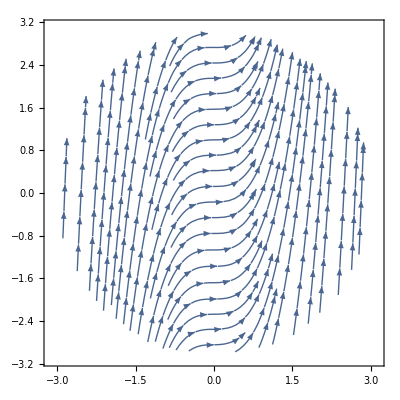

```mathematica
StreamPlot[
{1,3 x^2}
,{x,y}∈Disk[{0,0},3]]
```

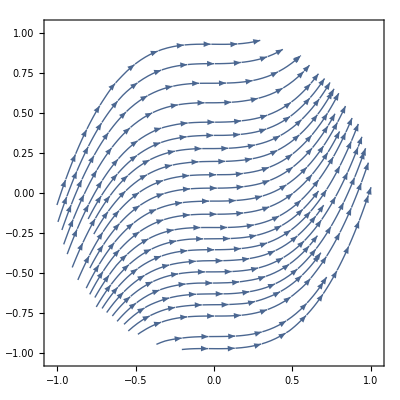

```mathematica
StreamPlot[
{1,3 x^2}
,{x,y}∈Disk[]]
```

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.Normalize@{1,3 x^2}==1
,{x,f'[x],f[x]}∈Reals]
```

√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x]

```mathematica
DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],{f[x]},{x}]
```

{{f[x]→x^3+C[1]}}

```mathematica
Trace@DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],{f[x]},{x}]
```

{{{√((1+9 x^4) (1+f'[x]^2)),√((1+9 x^4) (1+f'[x]^2))},√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x]},DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],{f[x]},{x}],{{f[x]→x^3+C[1]}}}

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.Normalize@{1,g'[x]}==1
,{x,f'[x],f[x],g'[x]}∈Reals]
```

√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]

```mathematica
DSolve[{√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],f[0]==0},{f[x]},{x}]
```

{{f[x]→-g[0]+g[x]}}

```mathematica
DSolve[{√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]},{f[x]},{x}]
```

{{f[x]→C[1]+g[x]}}

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.Normalize@{h'[x],g'[x]}==1
,{x,f'[x],f[x],g'[x],h'[x]}∈Reals]
```

(f'[x] g'[x]+h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1

```mathematica
DSolve[{(f'[x] g'[x]+h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1},{f[x]},{x}]
```

{{f[x]→C[1]+g'[K[1]]/h'[K[1]]K[1]1x}}

```mathematica
Activate[g'[K[1]]/h'[K[1]]K[1]1x]
```

∫_1^x g'[K[1]]/h'[K[1]]ⅆK[1]

```mathematica
∫_1^s g'[K[1]]/h'[K[1]] ⅆK[1]/.K[1]->x
```

∫_1^s g'[x]/h'[x]ⅆx

```mathematica
∫_1^s g'[x]/h'[x] ⅆx/.{h'[x]->1,g'[x]->3 x^2}
```

3 (-1/3+s^3/3)

```mathematica
Simplify[3 (-1/3+s^3/3)]
```

-1+s^3

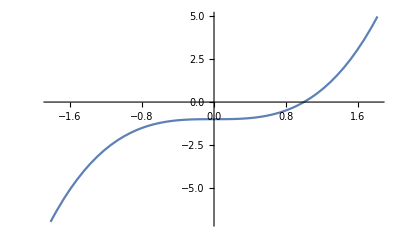

```mathematica
Plot[-1+s^3,{s,-1.8171205928321397,1.8171205928321397}]
```

```mathematica
Exp[f'[x]/f[x]]/.f->Function[x, x x]
```

ⅇ^(2/x)

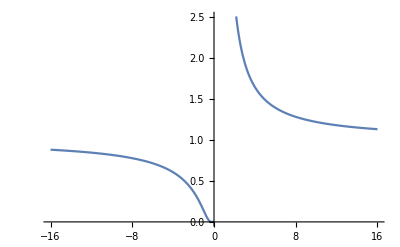

```mathematica
Plot[ⅇ^(2/x),{x,-16,16}]
```

```mathematica
Exp[f'[x]/f[x]]/.f->Function[x, 2^x]
```

2

```mathematica
Exp[f'[x]/f[x]]/.f->Exp
```

ⅇ

```mathematica
Solve[2 (G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2,{k},Reals]
```

{{k→-r-(√(r^2))/(√2)},{k→-r+(√(r^2))/(√2)}}

```mathematica
3 x^4-16 x^3+4 x^2+x
```

x+4 x^2-16 x^3+3 x^4

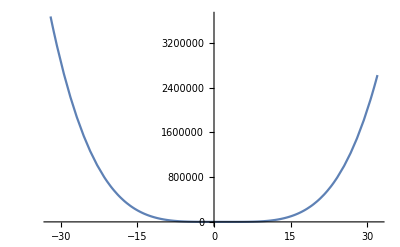

```mathematica
Plot[x+4 x^2-16 x^3+3 x^4,{x,-32.,32.}]
```

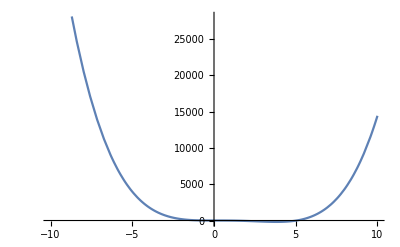

```mathematica
Plot[x+4 x^2-16 x^3+3 x^4,{x,-10,10}]
```

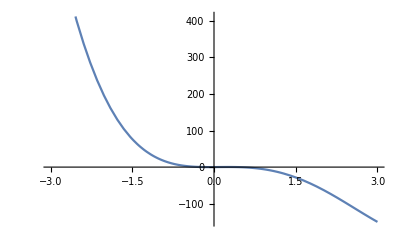

```mathematica
Plot[x+4 x^2-16 x^3+3 x^4,{x,-3,3}]
```

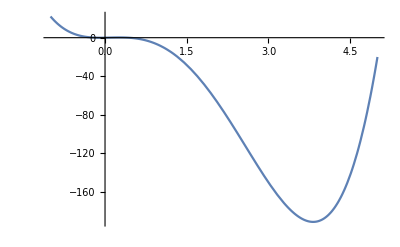

```mathematica
Plot[x+4 x^2-16 x^3+3 x^4,{x,-1,5}]
```

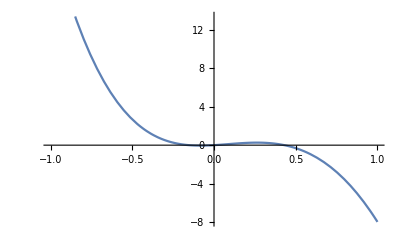

```mathematica
Plot[x+4 x^2-16 x^3+3 x^4,{x,-1,1}]
```

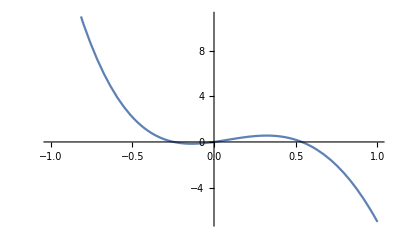

```mathematica
Plot[2x+4 x^2-16 x^3+3 x^4,{x,-1,1}]
```

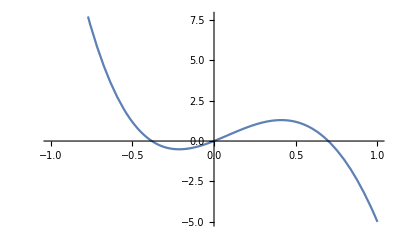

```mathematica
Plot[4x+4 x^2-16 x^3+3 x^4,{x,-1,1}]
```

```mathematica
Solve[4x+4 x^2-16 x^3+3 x^4,x,Reals]
```

Solve::naqs: 4 x+4 x^2-16 x^3+3 x^4 is not a quantified system of equations and inequalities.

Solve[4 x+4 x^2-16 x^3+3 x^4,x,ℝ]

```mathematica
Solve[4x+4 x^2-16 x^3+3 x^4==0,x,Reals]
```

{{x→0},{x→Root-0.380Root[4+4 #1-16 #1^2+3 #1^3&,1]-0.3802853684196638},{x→Root0.699Root[4+4 #1-16 #1^2+3 #1^3&,2]0.6992132948649827},{x→Root5.01Root[4+4 #1-16 #1^2+3 #1^3&,3]5.014405406888014}}

```mathematica
FullSimplify[
Normalize@D[{x,4 x+4 x^2-16 x^3+3 x^4},{x,2}].Normalize@D[{x,4 x+4 x^2-16 x^3+3 x^4},x]
,x∈Reals]
```

(16 (2+3 x (-8+3 x)) (1+x (2+3 (-4+x) x)))/(√((8+12 x (-8+3 x))^2 (1+(4+4 x (2+3 (-4+x) x))^2)))

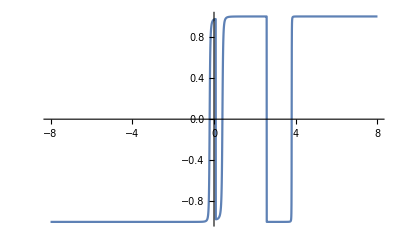

```mathematica
Plot[(16 (2+3 x (-8+3 x)) (1+x (2+3 (-4+x) x)))/(√((8+12 x (-8+3 x))^2 (1+(4+4 x (2+3 (-4+x) x))^2))),{x,-8,8}]
```

```mathematica
Solve[16 (2+3 x (-8+3 x)) (1+x (2+3 (-4+x) x))==0,x,Reals]
```

{{x→1/3 (4-√14)},{x→1/3 (4+√14)},{x→Root-0.213Root[1+2 #1-12 #1^2+3 #1^3&,1]-0.2130772740812874},{x→Root0.412Root[1+2 #1-12 #1^2+3 #1^3&,2]0.41150844804006886},{x→Root3.80Root[1+2 #1-12 #1^2+3 #1^3&,3]3.8015688260412186}}

```mathematica
D[{x,4 x+4 x^2-16 x^3+3 x^4},{x,2}]
```

{0,8-96 x+36 x^2}

```mathematica
Normalize@D[{x,4 x+4 x^2-16 x^3+3 x^4},{x,2}]
```

{0,(8-96 x+36 x^2)/Abs[8-96 x+36 x^2]}

```mathematica
1
```

1

```mathematica
8-96 x+36 x^2
```

8-96 x+36 x^2

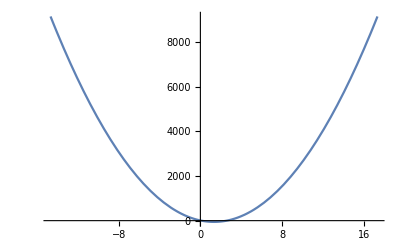

```mathematica
Plot[8-96 x+36 x^2,{x,-14.666666666666666,17.333333333333332}]
```

```mathematica
U=K-E
```

-ⅇ+K

```mathematica
K
```

K

```mathematica
Information[K]
```

```mathematica
D[1/2 m f'[x]^2==m g f[x],x]
```

m f'[x] f''[x]==g m f'[x]

```mathematica
0==D[1/2 m f'[x]^2==m g f[x],x]
```

0==(m f'[x] f''[x]==g m f'[x])

```mathematica
DSolve[0==(m f'[x] f''[x]==g m f'[x]),{f[x],f[x]},{x}]
```

DSolve[0==(m f'[x] f''[x]==g m f'[x]),{f[x],f[x]},{x}]

```mathematica
m f'[x] f''[x]-g m f'[x]==0
```

-g m f'[x]+m f'[x] f''[x]==0

```mathematica
DSolve[-g m f'[x]+m f'[x] f''[x]==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]},{f[x]→(g x^2)/2+C[1]+x C[2]}}

```mathematica
m f'[x] f''[x]+g m f'[x]==0
```

g m f'[x]+m f'[x] f''[x]==0

```mathematica
DSolve[g m f'[x]+m f'[x] f''[x]==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]},{f[x]→-(g x^2)/2+C[1]+x C[2]}}

```mathematica
-(9 x^2)/2+x+1
```

1+x-(9 x^2)/2

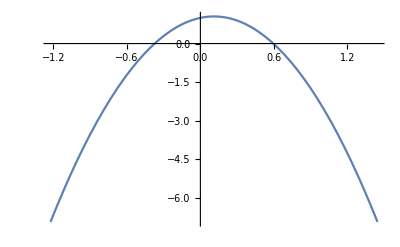

```mathematica
Plot[1+x-(9 x^2)/2,{x,-1.222222222222222,1.4444444444444444}]
```

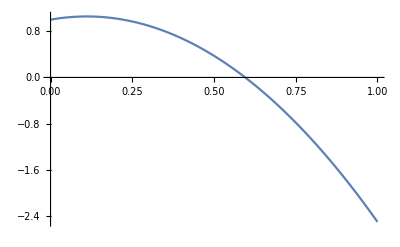

```mathematica
Plot[1+x-(9 x^2)/2,{x,0,1}]
```

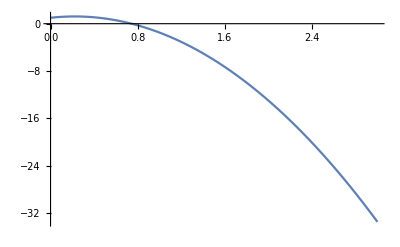

```mathematica
Plot[1+2x-(9 x^2)/2,{x,0,3}]
```

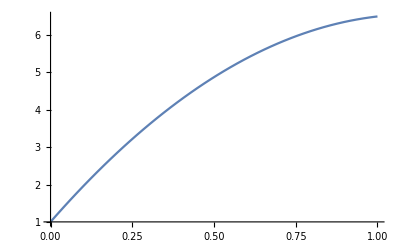

```mathematica
Plot[1+10x-(9 x^2)/2,{x,0,1}]
```

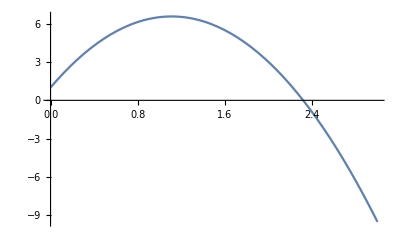

```mathematica
Plot[1+10x-(9 x^2)/2,{x,0,3}]
```

```mathematica
D[{x,1+10x-(9 x^2)/2},{x,2}]
```

{0,-9}

```mathematica
∫_a^b F[r[t]]Norm[r'[t]]ⅆt
```

∫_a^b F[r[t]] Norm[r'[t]]ⅆt

```mathematica
C[1]
```

C[1]

```mathematica
Table[C[i],{i,0,10}]
```

{C[0],C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10]}

```mathematica
v==d/t
```

v==d/t

```mathematica
Solve[v==d/t,t]
```

{{t→d/v}}

```mathematica
PositiveReals
```

```mathematica
Solve[1+10x-(9 x^2)/2,x,]
```

Solve::naqs: x>0&&1+10 x-(9 x^2)/2 is not a quantified system of equations and inequalities.

Solve[1+10 x-(9 x^2)/2,x,]

```mathematica
Solve[1+10x-(9 x^2)/2==0,x,]
```

{{x→1/9 (10+√118)}}

```mathematica
N[1/9 (10+√118)]
```

2.31809

```mathematica
Solve[D[1+10 x-(9 x^2)/2,x]==0,x,]
```

{{x→10/9}}

```mathematica
N[{{x->10/9}}]
```

{{x→1.11111}}

```mathematica
v==d/t
```

v==d/t

```mathematica
D[1+10 x-(9 x^2)/2,x]==(∫_0^(1/9 (10+√118)) √(1+D[1+10 x-(9 x^2)/2,x]^2)ⅆx)/t
```

10-9 x==(10 √101+√14042+ArcSinh[10]+ArcSinh[√118])/(18 t)

```mathematica
Dt[v==d/t]
```

Dt[v]==Dt[d]/t-(d Dt[t])/t^2

```mathematica
Dt[v[t]==d[t]/t]
```

Dt[t] v'[t]==-(d[t] Dt[t])/t^2+(Dt[t] d'[t])/t

```mathematica
Dt[f[t]==d[t]/t]
```

Dt[t] f'[t]==-(d[t] Dt[t])/t^2+(Dt[t] d'[t])/t

```mathematica
TraditionalForm[Dt[t] f'[t]==-(d[t] Dt[t])/t^2+(Dt[t] d'[t])/t]
```

ⅆt f'(t)==(ⅆt d'(t))/t-(d(t) ⅆt)/t^2

```mathematica
Dt[F[t]==Distance[t]/t]
```

Dt[t] F'[t]==-(Distance[t] Dt[t])/t^2+(Dt[t] Distance'[t])/t

```mathematica
TraditionalForm[Dt[t] F'[t]==-(Distance[t] Dt[t])/t^2+(Dt[t] Distance'[t])/t]
```

ⅆt F'(t)==(ⅆt Distance'(t))/t-(Distance(t) ⅆt)/t^2

```mathematica
D[1+10 t-(9 t^2)/2,t]==(∫_0^(1/9 (10+√118)) √(1+D[1+10 t-(9 t^2)/2,t]^2)ⅆt)/t
```

10-9 t==(10 √101+√14042+ArcSinh[10]+ArcSinh[√118])/(18 t)

```mathematica
Reduce[10-9 t==(10 √101+√14042+ArcSinh[10]+ArcSinh[√118])/(18 t)]
```

t==1/324 (180-ⅈ √(-32400+648 (10 √101+√14042+ArcSinh[10]+ArcSinh[√118])))||t==1/324 (180+ⅈ √(-32400+648 (10 √101+√14042+ArcSinh[10]+ArcSinh[√118])))

```mathematica
Reduce[10-9 t==(10 √101+√14042+ArcSinh[10]+ArcSinh[√118])/(18 t),t,Reals]
```

False

```mathematica
Reduce[10-9 t==a/(18 t)]
```

a==-18 (-10 t+9 t^2)&&t≠0

```mathematica
Reduce[10-9 t==a/(18 t),t]
```

(t==1/18 (10-√2 √(50-a))||t==1/18 (10+√2 √(50-a)))&&t≠0

```mathematica
Solve[{α x^3+β x^2==0,α+β==1},x,Reals]
```

{}

```mathematica
Solve[{α x^3+β x^2==0,α+β==1},x,Reals]
```

```mathematica
Solve[{α x^3+β x^2==1,α+β==1},x,Reals]
```

{}

```mathematica
Solve[{α x^3+β x^2==2,α+β==1},x,Reals]
```

{}

```mathematica
Solve[{α x^3+β x^2==2,α+β==1,x[1]==2},{α,β},Reals]
```

{}

```mathematica
Solve[{α x^3+β x^2==0,α+β==1,x[0]==0},{α,β},Reals]
```

{}

```mathematica
Solve[{α x^3+β x^2==1,α+β==1},{α,β},Reals]
```

{{α→(-x-x^2)/x^3,β→(1+x+x^2)/x^2}}

```mathematica
Solve[{f[x]==α x^3+β x^2==0,α+β==1},{α,β},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f[x]==x^3 α+x^2 β==0,α+β==1},{α,β},ℝ]

```mathematica
Solve[{f[x]==α x^3+β x^2,α+β==1},{α,β},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f[x]==x^3 α+x^2 β,α+β==1},{α,β},ℝ]

```mathematica
Solve[{f[x]==α x^3+β x^2,f[0]==0,α+β==1},{α,β},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f[x]==x^3 α+x^2 β,f[0]==0,α+β==1},{α,β},ℝ]

```mathematica
Solve[{f[x]==α x^3+β x^2,f[x]==1,α+β==1},{α,β},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f[x]==x^3 α+x^2 β,f[x]==1,α+β==1},{α,β},ℝ]

```mathematica
Solve[{α x^3+β x^2==1,α+β==1},{α,β},Reals]
```

{{α→(-x-x^2)/x^3,β→(1+x+x^2)/x^2}}

```mathematica
Solve[{α x^3+β x^2+γ x==1,α+β+γ==1},{α,β,γ},Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{α→(1-x^2 β-(x (1+x+x^2-x^2 β))/(x+x^2))/x^3,γ→(1+x+x^2-x^2 β)/(x+x^2)}}

```mathematica
Solve[{α x^3+β x^2+γ x==1,α+β+γ==1},{α,β},Reals]
```

{{α→(-x-x^2+x^2 γ)/x^3,β→(1+x+x^2-x γ-x^2 γ)/x^2}}

```mathematica
{{α->(-C[1]-C[2]+C[2] γ)/C[3],β->(C[0]+C[1]+C[2]-C[1] γ-C[2] γ)/C[2]}}
```

{{α→(-C[1]-C[2]+γ C[2])/C[3],β→(C[0]+C[1]-γ C[1]+C[2]-γ C[2])/C[2]}}

```mathematica
α[C[1],C[2],C[3],γ]
```

α[C[1],C[2],C[3],γ]

```mathematica
β[C[0],C[1],C[2],γ]
```

β[C[0],C[1],C[2],γ]

```mathematica
Solve[{α x^3+β x^2==1,α+β==1},{α,β},Reals]
```

{{α→(-x-x^2)/x^3,β→(1+x+x^2)/x^2}}

```mathematica
α[C[1],C[2],C[3]]
```

α[C[1],C[2],C[3]]

```mathematica
β[C[0],C[1],C[2]]
```

β[C[0],C[1],C[2]]

```mathematica
ContourPlot[x^3+x^2==1,{x,-2,2}]
```

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

ContourPlot[x^3+x^2==1,{x,-2,2}]

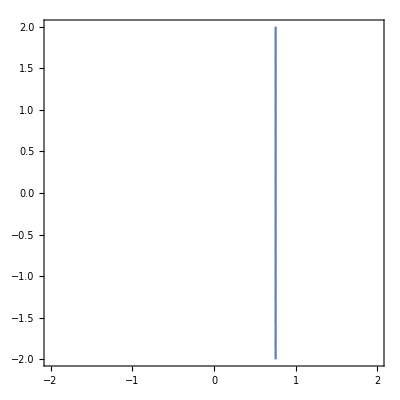

```mathematica
ContourPlot[x^3+x^2==1,{x,-2,2},{y,-2,2}]
```

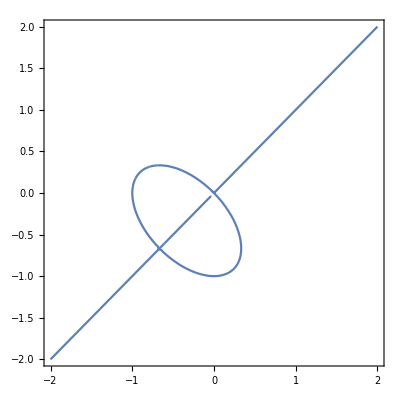

```mathematica
ContourPlot[x^3+x^2==y^3+y^2,{x,-2,2},{y,-2,2}]
```

```mathematica
Solve[{α x^3+β x^2+γ x==1,α+β+γ==1},{α,β,γ},Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{α→(1-x^2 β-(x (1+x+x^2-x^2 β))/(x+x^2))/x^3,γ→(1+x+x^2-x^2 β)/(x+x^2)}}

```mathematica
Solve[{α x^3+β x^2+γ x==1,α+β+γ==1,γ==1/2},{α,β,γ},Reals]
```

{{α→(1-x/2+1/2 (-2-x-x^2))/x^3,β→(2+x+x^2)/(2 x^2),γ→1/2}}

```mathematica
Solve[{α x^3+β x^2==1,α+β==1},{α,β},Reals]
```

{{α→(-x-x^2)/x^3,β→(1+x+x^2)/x^2}}

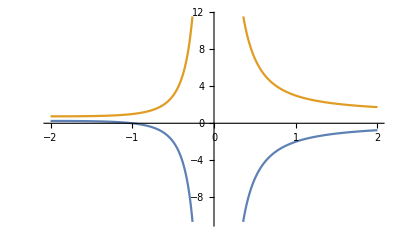

```mathematica
Plot[
{(-x-x^2)/x^3,(1+x+x^2)/x^2}
,{x,-2,2}]
```

```mathematica
f[x]==Abs[f[x]-C[1]]+C[2]
```

f[x]==Abs[-C[1]+f[x]]+C[2]

```mathematica
TraditionalForm[f[x]==Abs[f[x]-C[1]]+C[2]]
```

f(x)==Abs[f(x)-1]+2

```mathematica
f[x]==x^3+x^2
```

f[x]==x^2+x^3

```mathematica
Abs[x^3+x^2-x^3]+x^2
```

x^2+Abs[x]^2

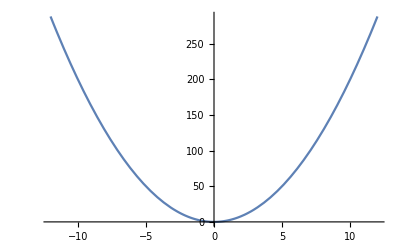

```mathematica
Plot[x^2+Abs[x]^2,{x,-12.,12.}]
```

```mathematica
x^3+x^2-x^3+x^3
```

x^2+x^3

```mathematica
Abs[x^3+x^2-x^3]+x^3
```

x^3+Abs[x]^2

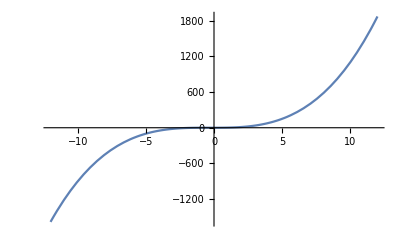

```mathematica
Plot[x^3+Abs[x]^2,{x,-12.,12.}]
```

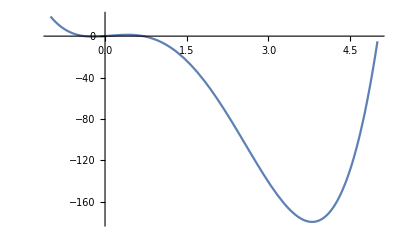

```mathematica
Plot[4x+4 x^2-16 x^3+3 x^4,{x,-1,5}]
```

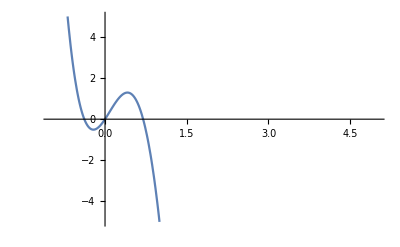

```mathematica
Plot[4x+4 x^2-16 x^3+3 x^4,{x,-1,5},PlotRange->{-5,5}]
```

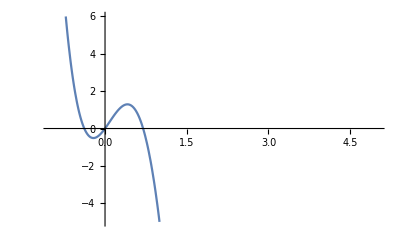

```mathematica
Plot[4x+4 x^2-16 x^3+3 x^4,{x,-1,5},PlotRange->{-5,6}]
```

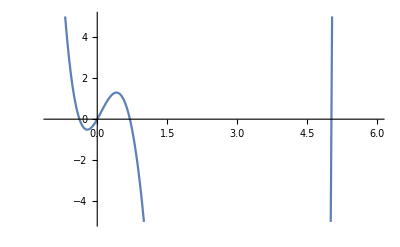

```mathematica
Plot[4x+4 x^2-16 x^3+3 x^4,{x,-1,6},PlotRange->{-5,5}]
```

```mathematica
Solve[D[4x+4 x^2-16 x^3+3 x^4,x]==0,x]
```

{{x→Root-0.213Root[1+2 #1-12 #1^2+3 #1^3&,1]-0.2130772740812874},{x→Root0.412Root[1+2 #1-12 #1^2+3 #1^3&,2]0.41150844804006886},{x→Root3.80Root[1+2 #1-12 #1^2+3 #1^3&,3]3.8015688260412186}}

```mathematica
D[4x+4 x^2-16 x^3+3 x^4,x][0]
```

(4+8 x-48 x^2+12 x^3)[0]

```mathematica
D[4x+4 x^2-16 x^3+3 x^4,x]/.x->0
```

4

```mathematica
D[4x+4 x^2-16 x^3+3 x^4,x]
```

4+8 x-48 x^2+12 x^3

```mathematica
D[4x+4 x^2-16 x^3+3 x^4,x]
```

4+8 x-48 x^2+12 x^3

```mathematica
4x+4 x^2-16 x^3+3 x^4
```

4 x+4 x^2-16 x^3+3 x^4

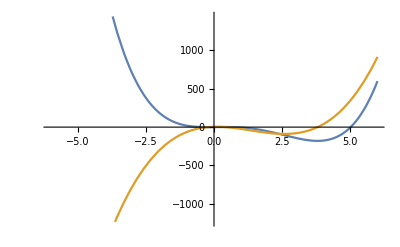

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,4+8 x-48 x^2+12 x^3}
,{x,-6,6}]
```

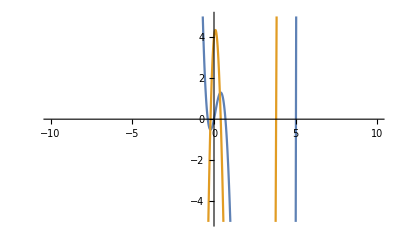

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,4+8 x-48 x^2+12 x^3}
,{x,-10,10}
,PlotRange->{-5,5}]
```

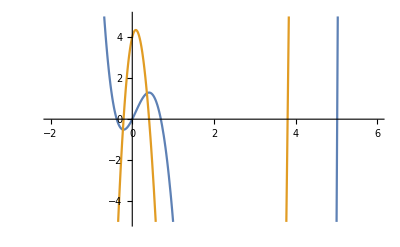

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,4+8 x-48 x^2+12 x^3}
,{x,-2,6}
,PlotRange->{-5,5}]
```

```mathematica
FullSimplify[Normalize@{x,4 x+4 x^2-16 x^3+3 x^4}.Normalize@{1,0},x∈Reals]
```

x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))

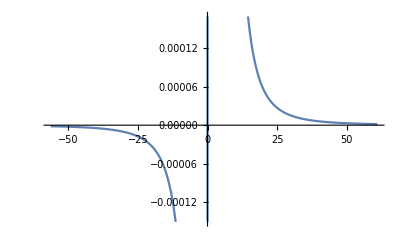

```mathematica
Plot[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),{x,-56.33195238838134,60.98877160062476}]
```

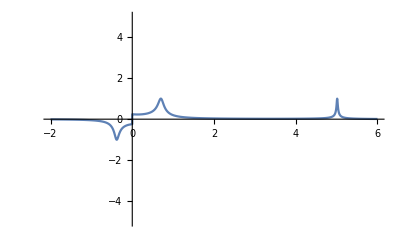

```mathematica
Plot[
x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),{x,-2,6},PlotRange->{-5,5}]
```

```mathematica
4 x+4 x^2-16 x^3+3 x^4
```

```mathematica
FullSimplify[Normalize@{x,4 x+4 x^2-16 x^3+3 x^4}.Normalize@{-1,0},x∈Reals]
```

-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2))

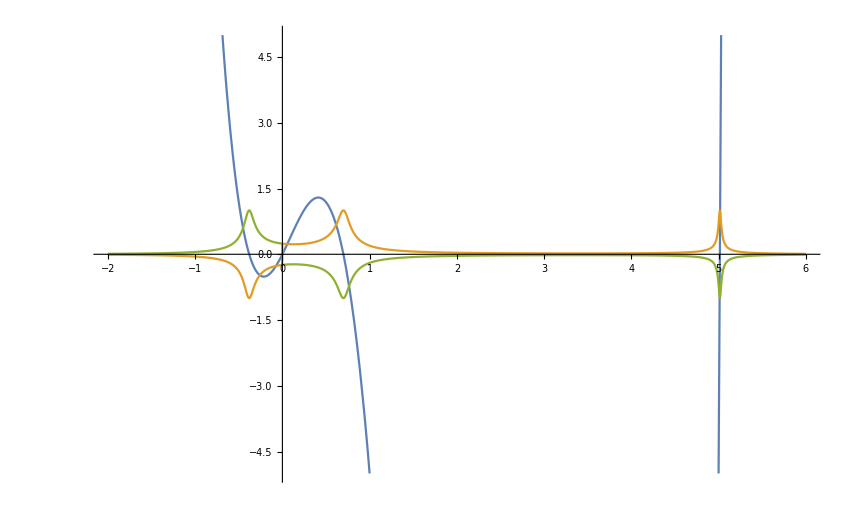

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2))}
,{x,-2,6}
,PlotRange->{-5,5}]
```

```mathematica
Integrate[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),x]==0
```

∫(x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)))ⅆx==0

```mathematica
Integrate[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),{x,-5,5}]-
Integrate[Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),{x,-5,5}]
```

∫_-5^5 x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))ⅆx-∫_-5^5 Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2))ⅆx

```mathematica
NIntegrate[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),{x,-5,5}]-
NIntegrate[Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),{x,-5,5}]
```

-5.27078×10^-14

```mathematica
NIntegrate[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),{x,-5,5}]
```

0.

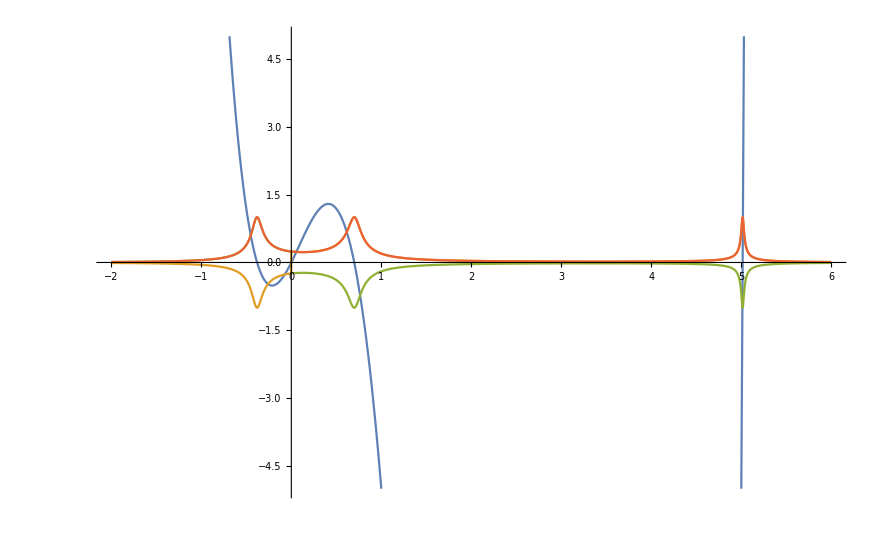

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),Abs[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))]}
,{x,-2,6}
,PlotRange->{-5,5}]
```

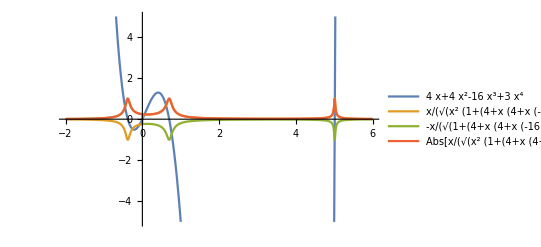

```mathematica
Plot[
{4 x+4 x^2-16 x^3+3 x^4,x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),-Sign[x]/(√(1+(4+x (4+x (-16+3 x)))^2)),Abs[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))]}
,{x,-2,6}
,PlotRange->{-5,5}
,PlotLegends->"Expressions"]
```

```mathematica
D[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),x]==0
```

1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))==0

```mathematica
Reduce[1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))==0]
```

x==2/9 (8-√55)||x==2/9 (8+√55)||x==Root-0.380Root[4+4 #1-16 #1^2+3 #1^3&,1]-0.3802853684196638||x==Root0.699Root[4+4 #1-16 #1^2+3 #1^3&,2]0.6992132948649827||x==Root5.01Root[4+4 #1-16 #1^2+3 #1^3&,3]5.014405406888014

```mathematica
Reduce[D[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))∧x≠0,x]==0,x,PositiveReals]
```

Reduce[(1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))&&∂_x (x≠0))==0,x,]

```mathematica
Reduce[D[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))∧x≠0,x]==0,x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))&&∂_x (x≠0))==0,x,ℝ]

```mathematica
Reduce[D[x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),x]==0,x,Reals]
```

x==0||x==1/9 (16-2 √55)||x==1/9 (16+2 √55)||x==Root-0.380Root[4+4 #1-16 #1^2+3 #1^3&,1]-0.3802853684196638||x==Root0.699Root[4+4 #1-16 #1^2+3 #1^3&,2]0.6992132948649827||x==Root5.01Root[4+4 #1-16 #1^2+3 #1^3&,3]5.014405406888014

```mathematica
TraditionalForm[1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))==0]
```

1/(√(x^2 ((x (x (3 x-16)+4)+4)^2+1)))-(x (2 (x (3 x-16)+x (6 x-16)+4) (x (x (3 x-16)+4)+4) x^2+2 ((x (x (3 x-16)+4)+4)^2+1) x))/(2 (x^2 ((x (x (3 x-16)+4)+4)^2+1))^(3/2))==0

```mathematica
1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))
```

1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))

```mathematica
FullSimplify[1/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))-(x (2 x^2 (4+x (-16+3 x)+x (-16+6 x)) (4+x (4+x (-16+3 x)))+2 x (1+(4+x (4+x (-16+3 x)))^2)))/(2 (x^2 (1+(4+x (4+x (-16+3 x)))^2))^(3/2))]
```

-(x^3 (4+x (-32+9 x)) (4+x (4+x (-16+3 x))))/((x^2 (17+x (4+x (-16+3 x)) (8+x (4+x (-16+3 x)))))^(3/2))

```mathematica
Reduce[-x^3 (4+x (-32+9 x)) (4+x (4+x (-16+3 x)))==0,x,Reals]
```

x==0||x==1/9 (16-2 √55)||x==1/9 (16+2 √55)||x==Root-0.380Root[4+4 #1-16 #1^2+3 #1^3&,1]-0.3802853684196638||x==Root0.699Root[4+4 #1-16 #1^2+3 #1^3&,2]0.6992132948649827||x==Root5.01Root[4+4 #1-16 #1^2+3 #1^3&,3]5.014405406888014

```mathematica
ExpandAll[-x^3 (4+x (-32+9 x)) (4+x (4+x (-16+3 x)))]
```

-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8

```mathematica
FullSimplify[Normalize[{x,x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2)))}],x∈Reals]
```

{x/(√(x^2+1/(1+(4+x (4+x (-16+3 x)))^2))),x/(√(x^2+x^4 (17+x (4+x (-16+3 x)) (8+x (4+x (-16+3 x))))))}

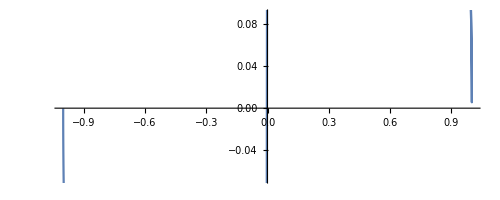

```mathematica
ParametricPlot[
{x/(√(x^2+1/(1+(4+x (4+x (-16+3 x)))^2))),x/(√(x^2+x^4 (17+x (4+x (-16+3 x)) (8+x (4+x (-16+3 x))))))}
,{x,-5,5}]
```

```mathematica
ParametricPlot[
{x/(√(x^2+1/(1+(4+x (4+x (-16+3 x)))^2))),x/(√(x^2+x^4 (17+x (4+x (-16+3 x)) (8+x (4+x (-16+3 x))))))}
,{x,-5,5}]
```

```mathematica
4 x+4 x^2-16 x^3+3 x^4
```

```mathematica
FullSimplify[Normalize[{x,4 x+4 x^2-16 x^3+3 x^4}],x∈Reals]
```

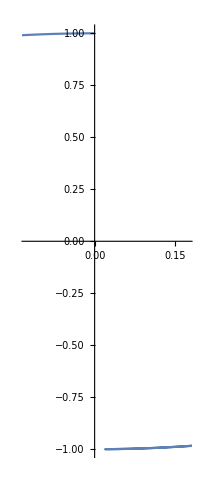

```mathematica
ParametricPlot[
{x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),((4+x (4+x (-16+3 x))) Sign[x])/(√(1+(4+x (4+x (-16+3 x)))^2))}
,{x,-5,5}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,4 x+4 x^2-16 x^3+3 x^4},
{x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),((4+x (4+x (-16+3 x))) Sign[x])/(√(1+(4+x (4+x (-16+3 x)))^2))}
},{x,-2,-2+α}]
,{α,0,10}]
```

ParametricPlot::plld: Endpoints for x in {x,-2,-2+FE`α$$553} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for x in {x,-2,-2+FE`α$$553} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[{
{x,4 x+4 x^2-16 x^3+3 x^4},
{x/(√(x^2 (1+(4+x (4+x (-16+3 x)))^2))),((4+x (4+x (-16+3 x))) Sign[x])/(√(1+(4+x (4+x (-16+3 x)))^2))}
},{x,-2,-2+α}
,PlotRange->{{-2,2},{-2,2}}]
,{α,0,10}]
```

ParametricPlot::plld: Endpoints for x in {x,-2,-2+FE`α$$557} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8
```

-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8

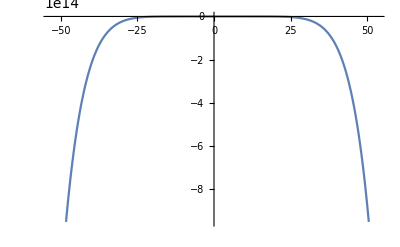

```mathematica
Plot[-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8,{x,-53.33333333333333,53.33333333333333}]
```

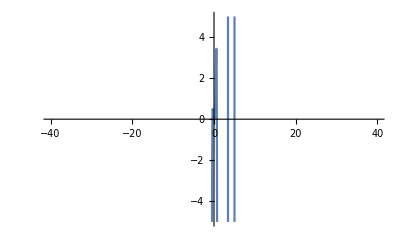

```mathematica
Plot[-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8,{x,-40,40},PlotRange->{-5,5}]
```

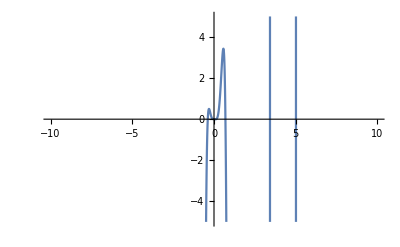

```mathematica
Plot[-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8,{x,-10,10},PlotRange->{-5,5}]
```

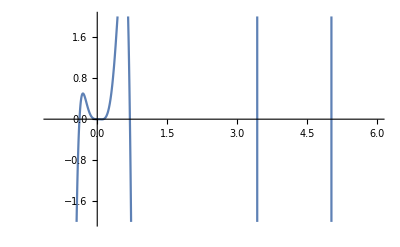

```mathematica
Plot[-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8,{x,-1,6},PlotRange->{-2,2}]
```

```mathematica
(1-a)p+a q/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
```

√(Abs[(1-a) t+a Cos[t]]^2+Abs[(1-a) t+a Sin[t]]^2)

```mathematica
FullSimplify[Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,t}∈Reals]
```

√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)

```mathematica
Manipulate[Plot[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,-0.635207997567232,0.6352079895671068}],{a,0,1}]
```

```mathematica
Plot3D[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
FindMinimum[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,4}]
```

FindMinimum::nrnum: The function value √((4.-4.7568 a)^2+(4.-4.65364 a)^2) is not a real number at {t} = {4.}.

FindMinimum[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,4}]

```mathematica
FindMinimum[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,4},{a,8/10}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{8.5552×10^-15,{t→3.92699,a→0.847412}}

```mathematica
(1-a)p+a q/.{p->{x,-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8},q->{x,D[-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8,x]}}
```

{(1-a) x+a x,a (-48 x^2+448 x^3+780 x^4-3360 x^5+1680 x^6-216 x^7)+(1-a) (-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8)}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) x+a x,a (-48 x^2+448 x^3+780 x^4-3360 x^5+1680 x^6-216 x^7)+(1-a) (-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8)}
,{x,-1,6}],{a,0,1}]
```

```mathematica
Plot3D[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

```mathematica
ParametricPlot3D[
{(1-a) x+a x,a (-48 x^2+448 x^3+780 x^4-3360 x^5+1680 x^6-216 x^7)+(1-a) (-16 x^3+112 x^4+156 x^5-560 x^6+240 x^7-27 x^8)}
,{x,-1,6},{a,0,1}]
```

-Graphics3D-

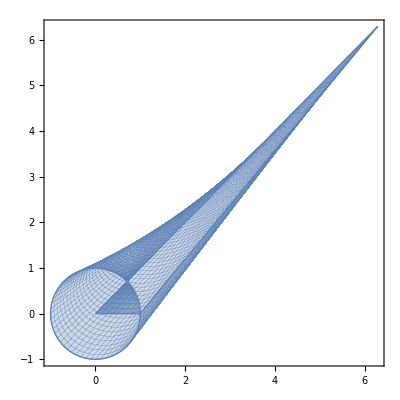

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π}],{a,0,1}]
```

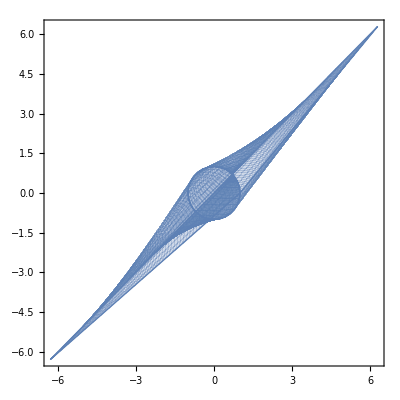

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-2π,2π},{a,0,1}]
```

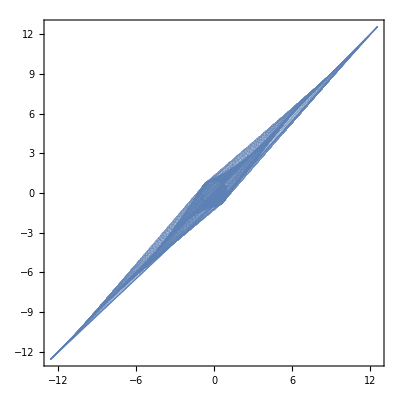

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-4π,4π},{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-2π,2π},{a,0.0001,b}]
,{b,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-8π,8π},{a,0.0001,b}]
,{b,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-8π,8π},{a,0.0001,b}
,PlotRange->{{-2,2},{-2,2}}]
,{b,0,1}]
```

```mathematica
FullSimplify[Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{t,a}∈Reals∧0≤t≤2π∧0≤a≤1]
```

√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)

```mathematica
Manipulate[Plot[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π}],{a,0,1}]
```

```mathematica
Integrate[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{a,0,1}]
```

$Aborted

```mathematica
Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}]
```

{t/2+Cos[t]/2,t/2+Sin[t]/2}

```mathematica
Integrate[{t/2+Cos[t]/2,t/2+Sin[t]/2},{t,0,2π}]
```

{π^2,π^2}

```mathematica
Norm@{π^2,π^2}
```

√2 π^2

```mathematica
N[√2 π^2]
```

13.9577

```mathematica
NIntegrate[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

14.7543

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
NIntegrate[Norm[{-t+Cos[t],-t+Sin[t]}],{t,0,2π}]
```

28.9736

```mathematica
Norm@Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]==2α NIntegrate[Norm[{-t+Cos[t],-t+Sin[t]}],{t,0,2π}]
```

√2 π^2==57.9471 α

```mathematica
Solve[
Norm@Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]==2α NIntegrate[Norm[{-t+Cos[t],-t+Sin[t]}],{t,0,2π}],α]
```

{{α→0.24087}}

```mathematica
Norm@Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]
```

√2 π^2

```mathematica
N[√2 π^2]
```

13.9577

```mathematica
N@Norm@Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]
```

13.9577

```mathematica
Integrate[Integrate[Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]
```

$Aborted

```mathematica
NIntegrate[Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1},{t,0,2π}]
```

14.7543

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

-Graphics-

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.t->0
```

{a,0}

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.t->2π
```

{a+2 (1-a) π,2 (1-a) π}

```mathematica
Manipulate[Plot[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π}],{a,0,1}]
```

```mathematica
Plot3D[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.t->4
```

{4 (1-a)+a Cos[4],4 (1-a)+a Sin[4]}

```mathematica
D[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)
```

```mathematica
Plot3D[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
(1-a)p+a q/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
```

√(Abs[(1-a) t+a Cos[t]]^2+Abs[(1-a) t+a Sin[t]]^2)

```mathematica
ExpandAll[FullSimplify[Norm@{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{t,a}∈Reals]]
```

√(2 t^2-4 a t^2+2 a^2 t^2+2 a t Cos[t]-2 a^2 t Cos[t]+a^2 Cos[t]^2+2 a t Sin[t]-2 a^2 t Sin[t]+a^2 Sin[t]^2)

```mathematica
Manipulate[Plot[√(2 t^2-4 a t^2+2 a^2 t^2+2 a t Cos[t]-2 a^2 t Cos[t]+a^2 Cos[t]^2+2 a t Sin[t]-2 a^2 t Sin[t]+a^2 Sin[t]^2),{t,-0.6351656785224551,0.6351656726783308}],{a,-0.6351656700605757,0.6351656811402102}]
```

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
FullSimplify[Norm@{-t+Cos[t],-t+Sin[t]},t∈Reals]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

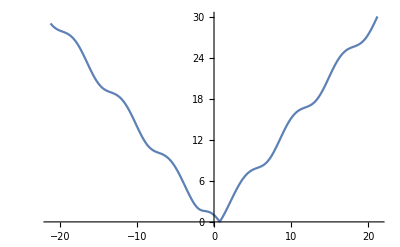

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-21.205750411731103,21.205750411731103}]
```

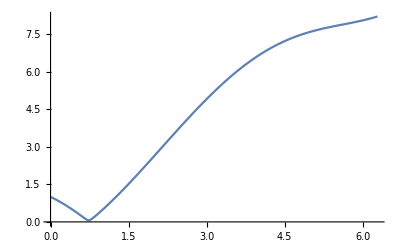

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

$Aborted

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
N@(28.973554590759658/2)
```

14.4868

```mathematica
{t,3}-{t,1}
```

{0,2}

```mathematica
Norm@{0,2}
```

2

```mathematica
Integrate[2,{t,0,1},{a,0,1}]
```

2

```mathematica
(1-a)p+a q/.{p->{t,1},q->{t,3}}
```

{(1-a) t+a t,1+2 a}

```mathematica
Norm@{(1-a) t+a t,1+2 a}
```

√(Abs[1+2 a]^2+Abs[(1-a) t+a t]^2)

```mathematica
FullSimplify[Norm@{(1-a) t+a t,1+2 a},{a,t}∈Reals]
```

√((1+2 a)^2+t^2)

```mathematica
Manipulate[Plot[√((1+2 a)^2+t^2),{t,-0.5938232422160856,0.5938232422160856}],{a,-1.118823242216084,0.06882324221608715}]
```

```mathematica
Integrate[FullSimplify[Norm@{(1-a) t+a t,1+2 a},{a,t}∈Reals],{a,0,1},{t,0,1}]
```

$Aborted

```mathematica
NIntegrate[FullSimplify[Norm@{(1-a) t+a t,1+2 a},{a,t}∈Reals],{a,0,1},{t,0,1}]
```

2.08684

```mathematica
FullSimplify[Norm@NIntegrate[{(1-a) t+a t,1+2 a},{a,0,1},{t,0,1}],{a,t}∈Reals]
```

2.06155

```mathematica
a-a
```

0

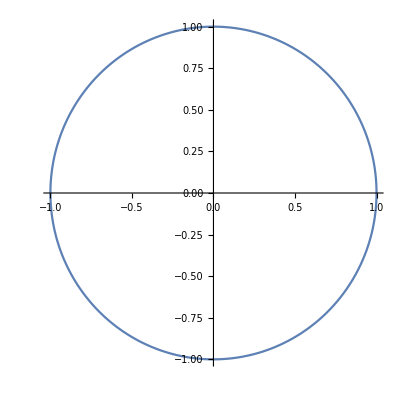

```mathematica
ParametricPlot[
{Sin[t],Cos[t]}
,{t,0,2π}]
```

```mathematica
(1-a)p+a q/.{p->{Cos[t],Sin[t]},q->{Sin[t],Cos[t]}}
```

{(1-a) Cos[t]+a Sin[t],a Cos[t]+(1-a) Sin[t]}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) Cos[t]+a Sin[t],a Cos[t]+(1-a) Sin[t]}
,{t,0,2π}]
,{a,0,1}]
```

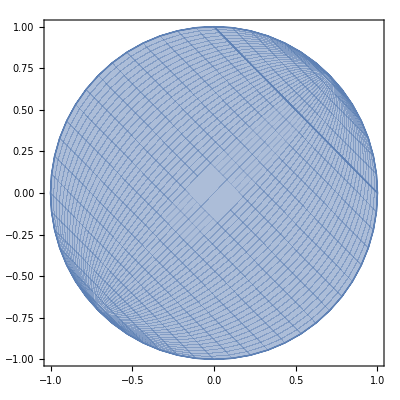

```mathematica
ParametricPlot[
{(1-a) Cos[t]+a Sin[t],a Cos[t]+(1-a) Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) Cos[t]+a Sin[t],a Cos[t]+(1-a) Sin[t]}
,{t,0,2π},{a,0.01,b}]
,{b,0,1}]
```

```mathematica
{Sin[t],Cos[t]}-{Cos[t],Sin[t]}
```

{-Cos[t]+Sin[t],Cos[t]-Sin[t]}

```mathematica
Norm@{-Cos[t]+Sin[t],Cos[t]-Sin[t]}
```

√(Abs[Cos[t]-Sin[t]]^2+Abs[-Cos[t]+Sin[t]]^2)

```mathematica
FullSimplify[Norm@{-Cos[t]+Sin[t],Cos[t]-Sin[t]},t∈Reals]
```

√(2-4 Cos[t] Sin[t])

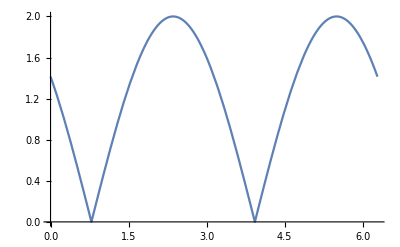

```mathematica
Plot[√(2-4 Cos[t] Sin[t]),{t,0,2π}]
```

```mathematica
Integrate[√(2-4 Cos[t] Sin[t]),{t,0,2π}]
```

8

```mathematica
8==π r^2
```

8==π r^2

```mathematica
Reduce[8==π r^2]
```

r==-2 √(2/π)||r==2 √(2/π)

```mathematica
2π r^2==2π (r+k)^2
```

2 π r^2==2 π (k+r)^2

```mathematica
Reduce[2 π r^2==2 π (k+r)^2,k,Reals]
```

(r<0&&(k==0||k==-2 r))||(r==0&&k==0)||(r>0&&(k==-2 r||k==0))

```mathematica
Reduce[2 π r^2==2 π (k+r)^2∧r>0,k,Reals]
```

r>0&&(k==-2 r||k==0)

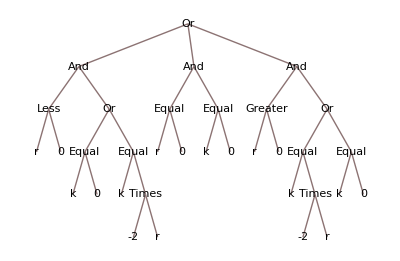

```mathematica
TreeForm[(r<0&&(k==0||k==-2 r))||(r==0&&k==0)||(r>0&&(k==-2 r||k==0))]
```

```mathematica
Abs[Sin[x]]
```

Abs[Sin[x]]

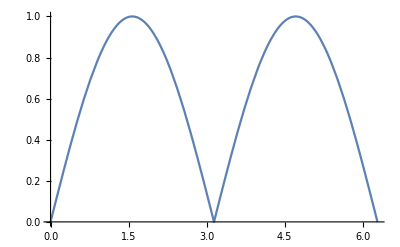

```mathematica
Plot[Abs[Sin[x]],{x,0,2π}]
```

```mathematica
Reduce[Abs[Sin[x]]==0∧x>0,x,Reals]
```

C[1]∈ℤ&&((C[1]≥1&&x==2 π C[1])||(C[1]≥0&&x==π+2 π C[1]))

```mathematica
Integrate[Abs[Sin[x]],{x,0,π}]
```

2

```mathematica
α Hold@Integrate[Abs[Sin[x]],{x,0,π}]
```

α Hold[∫_0^π Abs[Sin[x]]ⅆx]

```mathematica
Hold[α Integrate[Abs[Sin[x]],{x,0,π}]]
```

Hold[α ∫_0^π Abs[Sin[x]]ⅆx]

```mathematica
Inactivate[α Integrate[Abs[Sin[x]],{x,0,π}]]
```

α*Abs[Sin[x]]x0π

```mathematica
TraditionalForm[Inactivate[α Integrate[Abs[Sin[x]],{x,0,π}]]]
```

α*Abs(sin(x))x0π

```mathematica
α Integrate[Abs[Sin[x]],{x,0,π}]==Integrate[Abs[Sin[x]],{x,0,a}]
```

ConditionalExpression[2 α==2 IntegerPart[a/π]+(1-Cos[π FractionalPart[a/π]]) Sign[FractionalPart[a/π]],a∈ℝ]

```mathematica
FullSimplify[α Integrate[Abs[Sin[x]],{x,0,π}]==Integrate[Abs[Sin[x]],{x,0,a}],{α,a}∈]
```

2 α+(-1+Cos[π FractionalPart[a/π]]) Sign[FractionalPart[a/π]]==2 IntegerPart[a/π]

```mathematica
PositiveReals
```

```mathematica
Solve[FullSimplify[α Integrate[Abs[Sin[x]],{x,0,π}]==Integrate[Abs[Sin[x]],{x,0,a}],{α,a}∈],α,PositiveReals]
```

{{α→ConditionalExpression[1/2 (1-Cos[π FractionalPart[a/π]]+2 IntegerPart[a/π]),(0<FractionalPart[a/π]<1/2&&IntegerPart[a/π]>0)||(C[1]∈ℤ&&1/2 (-1+4 C[1])<FractionalPart[a/π]<1/2 (1+4 C[1])&&C[1]≥1&&IntegerPart[a/π]>0)]}}

```mathematica
FractionalPart[x]
```

FractionalPart[x]

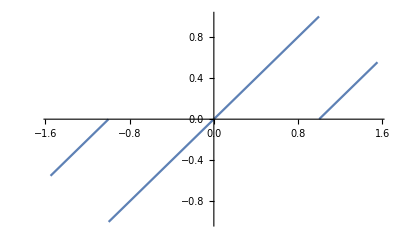

```mathematica
Plot[FractionalPart[x],{x,-1.5508771774946717,1.5537822825867664}]
```

```mathematica
TraditionalForm@{{α->ConditionalExpression[1/2 (1-Cos[π FractionalPart[a/π]]+2 IntegerPart[a/π]),(0<FractionalPart[a/π]<1/2&&IntegerPart[a/π]>0)||(C[1]∈Integers&&1/2 (-1+4 C[1])<FractionalPart[a/π]<1/2 (1+4 C[1])&&C[1]≥1&&IntegerPart[a/π]>0)]}}
```

{{α→ConditionalExpression[1/2 (2 IntegerPart[a/π]-cos(π frac(a/π))+1),(0<frac(a/π)<1/2∧IntegerPart[a/π]>0)∨(1∈ℤ∧1/2 (4 1-1)<frac(a/π)<1/2 (4 1+1)∧1≥1∧IntegerPart[a/π]>0)]}}

```mathematica
Solve[FullSimplify[α Integrate[Abs[Sin[x]],{x,0,π}]==Integrate[Abs[Sin[x]],{x,0,a}],{α,a}∈],α]
```

{{α→1/2 (2 IntegerPart[a/π]+Sign[FractionalPart[a/π]]-Cos[π FractionalPart[a/π]] Sign[FractionalPart[a/π]])}}

```mathematica
1/2 (2 IntegerPart[a/π]+Sign[FractionalPart[a/π]]-Cos[π FractionalPart[a/π]] Sign[FractionalPart[a/π]])
```

1/2 (2 IntegerPart[a/π]+Sign[FractionalPart[a/π]]-Cos[π FractionalPart[a/π]] Sign[FractionalPart[a/π]])

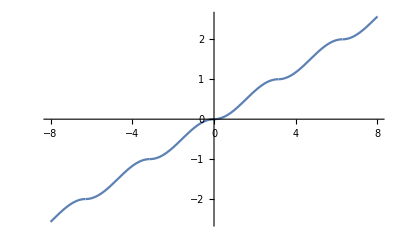

```mathematica
Plot[1/2 (2 IntegerPart[a/π]+Sign[FractionalPart[a/π]]-Cos[π FractionalPart[a/π]] Sign[FractionalPart[a/π]]),{a,-8,8}]
```

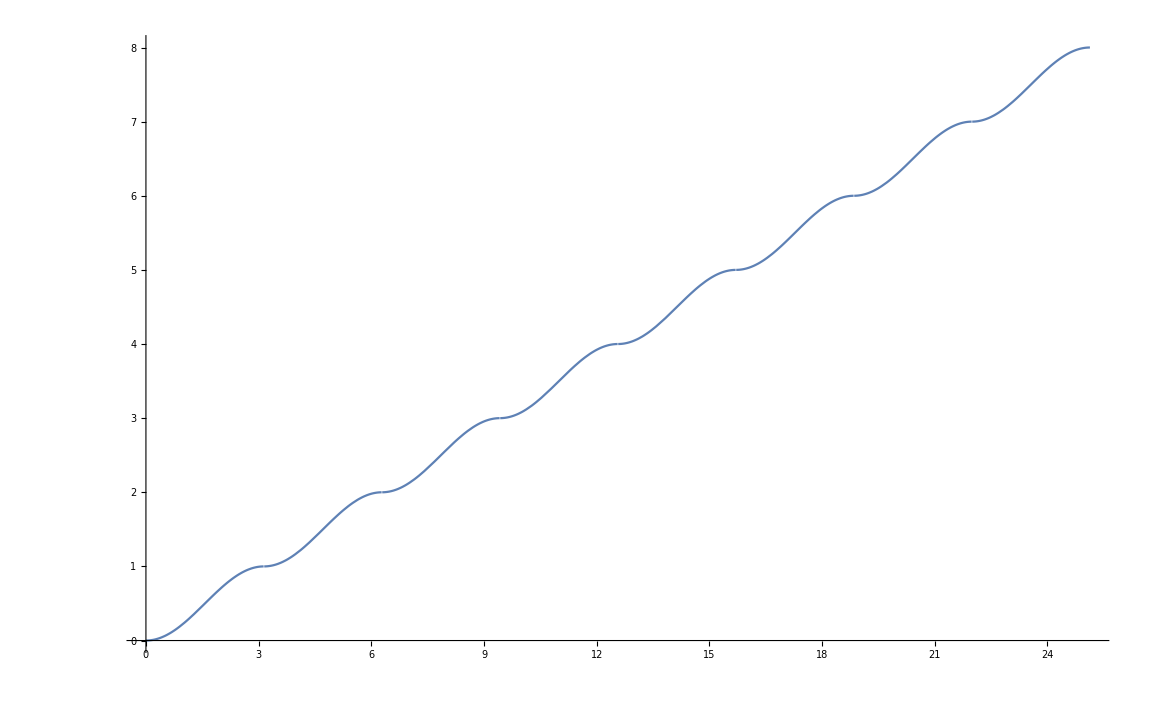

```mathematica
Plot[1/2 (2 IntegerPart[a/π]+Sign[FractionalPart[a/π]]-Cos[π FractionalPart[a/π]] Sign[FractionalPart[a/π]]),{a,0,8π}]
```

```mathematica
Sin[x]+x^3
```

x^3+Sin[x]

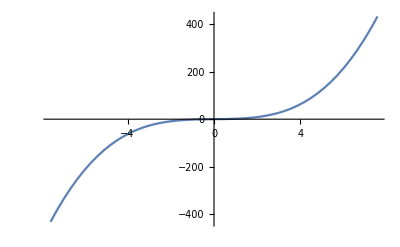

```mathematica
Plot[x^3+Sin[x],{x,-7.55952629936924,7.55952629936924}]
```

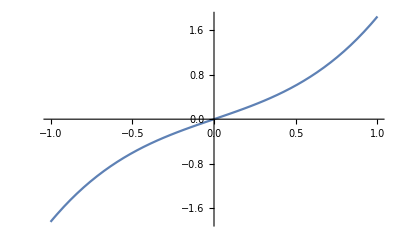

```mathematica
Plot[x^3+Sin[x],{x,-1,1}]
```

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
f[x]/Dt[x]
```

f[x]/Dt[x]

```mathematica
f[x]/Dt[x]==f'[x]
```

f[x]/Dt[x]==f'[x]

```mathematica
f[x]/Dt[x]==f'[x]/.x->g[x]
```

f[g[x]]/(Dt[x] g'[x])==f'[g[x]]

```mathematica
Dt[x] f[g[x]]/(Dt[x] g'[x]) g[x]/Dt[x]
```

(f[g[x]] g[x])/(Dt[x] g'[x])

```mathematica
Dt[x] f[g[x]]/Dt[x] g[x]/Dt[x] Power[g[x]/Dt[x],-1]
```

f[g[x]]

```mathematica
Solve[d[f[x]]/d[x]==f'[x],d[f[x]]]
```

{{d[f[x]]→d[x] f'[x]}}

```mathematica
Integrate[d[f[x]]==d[x] f'[x],x]
```

∫(d[f[x]]==d[x] f'[x])ⅆx

```mathematica
Integrate[d[f[x]],x]==Integrate[d[x] f'[x],x]
```

∫d[f[x]]ⅆx==∫d[x] f'[x]ⅆx

```mathematica
DSolve[∫d[f[x]]ⅆx==∫d[x] f'[x]ⅆx,{f[x]},{x}]
```

DSolve[∫d[f[x]]ⅆx==∫d[x] f'[x]ⅆx,{f[x]},{x}]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Integrate[Dt[f[x]],x]==Integrate[Dt[x] f'[x],x]
```

True

```mathematica
Integrate[Dt[x] f'[x],x]
```

∫Dt[x] f'[x]ⅆx

```mathematica
Integrate[Dt[x] f'[x],Dt[x]]
```

1/2 Dt[x]^2 f'[x]

```mathematica
Dt[f[g[h[x]]]]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]/.{f->Function[x,1/(√x)]}
```

-(Dt[x] g'[h[x]] h'[x])/(2 g[h[x]]^(3/2))

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]/.{f->Function[x,1/(√x)],g->Function[x,x+1]}
```

-(Dt[x] h'[x])/(2 (1+h[x])^(3/2))

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]/.{f->Function[x,1/(√x)],g->Function[x,x+1],h->Function[x, x x]}
```

-(x Dt[x])/((1+x^2)^(3/2))

```mathematica
TraditionalForm[-(x Dt[x])/((1+x^2)^(3/2))]
```

-(x ⅆx)/((x^2+1)^(3/2))

```mathematica
f[g[h[x]]]/.{f->Function[x,1/(√x)],g->Function[x,x+1],h->Function[x, x x]}
```

1/(√(1+x^2))

```mathematica
D[1/(√(1+x^2)), x]
```

-x/((1+x^2)^(3/2))

```mathematica
D[(-x/((1+x^2)^(3/2))), x]
```

(3 x^2)/((1+x^2)^(5/2))-1/((1+x^2)^(3/2))

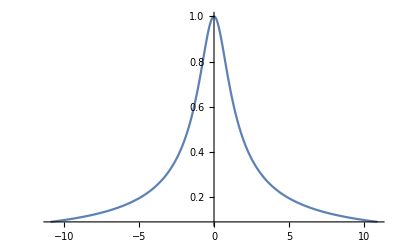

```mathematica
Plot[1/(√(1+x^2)),{x,-10.92,10.92}]
```

```mathematica
D[{1/(√x),x+1,x^2},x]
```

{-1/(2 x^(3/2)),1,2 x}

```mathematica
Integrate[-1/(2 x^(3/2)),x]
```

1/(√x)

```mathematica
Dt[f[g[h[x]]]]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
Solve[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),f[x]]
```

{}

```mathematica
Solve[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),f'[x]]
```

{}

```mathematica
DSolve[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),{f[x]},{x}]
```

DSolve[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),{f[x]},{x}]

```mathematica
DSolve[f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),{f[x]},{x}]
```

DSolve[f'[g[h[x]]] g'[h[x]] h'[x]==-x/((1+x^2)^(3/2)),{f[x]},{x}]

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
ApplySides[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==a,Identity]
```

ApplySides[Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==a,Identity]

```mathematica
(Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==a)/Dt[x]
```

(Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==a)/Dt[x]

```mathematica
f'[g[h[x]]] g'[h[x]] h'[x]==a Dt[x]
```

f'[g[h[x]]] g'[h[x]] h'[x]==a Dt[x]

```mathematica
Integrate[f'[g[h[x]]],x]==(a Dt[x])/(g'[h[x]] h'[x])
```

∫f'[g[h[x]]]ⅆx==(a Dt[x])/(g'[h[x]] h'[x])

```mathematica
Integrate[f'[g[h[x]]],x]==Integrate[a/(g'[h[x]] h'[x]),x]
```

∫f'[g[h[x]]]ⅆx==a ∫1/(g'[h[x]] h'[x])ⅆx

```mathematica
Integrate[f'[g[h[x]]],x]==Integrate[Integrate[a/(g'[h[x]] h'[x]),x],x]
```

∫f'[g[h[x]]]ⅆx==a ∫(∫1/(g'[h[x]] h'[x])ⅆx)ⅆx

```mathematica
Dt[f[x] g[h[x]]]
```

Dt[x] g[h[x]] f'[x]+Dt[x] f[x] g'[h[x]] h'[x]

```mathematica
Integrate[f'[g[h[x]]] g'[h[x]] h'[x],x]==f[g[h[x]]]
```

True

```mathematica
Integrate[f'[g[h[x]]] g'[h[x]] h'[x],x]
```

f[g[h[x]]]

```mathematica
Integrate[g[h[x]] f'[x]+Dt[x] f[x] g'[h[x]] h'[x],x]
```

∫(g[h[x]] f'[x]+Dt[x] f[x] g'[h[x]] h'[x])ⅆx

```mathematica
Integrate[g[h[x]] f'[x]+f[x] g'[h[x]] h'[x],x]
```

f[x] g[h[x]]

```mathematica
Dt@Dt@f@x
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Integrate[Integrate[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x],x],x]
```

∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx

```mathematica
∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx==f[x]
```

∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx==f[x]

```mathematica
Dt[x] f[x]/Dt[x] g[x]/f[x]
```

g[x]

```mathematica
Cross[{a,b,c},{d,e,f}]
```

{-c e+b f,c d-a f,-b d+a e}

```mathematica
Cross[{a,b,c},{d,e,0}]
```

{-c e,c d,-b d+a e}

```mathematica
Cross[{a,0,c},{d,e,0}]
```

{-c e,c d,a e}

```mathematica
Cross[{a,0,c},{0,e,0}]
```

{-c e,0,a e}

```mathematica
{-c e,0,a e}.{0,e,0}
```

0

```mathematica
{-c e,0,a e}.{a,0,c}
```

0

```mathematica
FindGeometricTransform[{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}]
```

{1.2254×10^-11,TransformationFunction[(-0.532365 | -0.665026 | 60.0196
-0.652893 | -0.649893 | 65.0385
-0.0097298 | -0.0105744 | 1.)]}

```mathematica
ListPlot[{{88, 59}, {96, 11}, {66, 2}, {54, 62}}, {{70, 20}, {12, 89}, {35, 65}, {68, 59}}]
```

ListPlot[{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}]

```mathematica
DiscretePlot[{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}]
```

DiscretePlot[{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}]

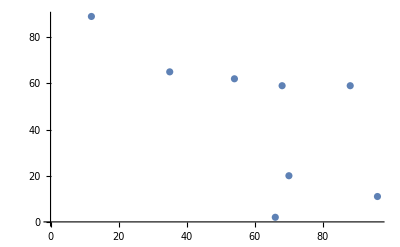

```mathematica
ListPlot[{{88,59},{96,11},{66,2},{54,62},{70,20},{12,89},{35,65},{68,59}}]
```

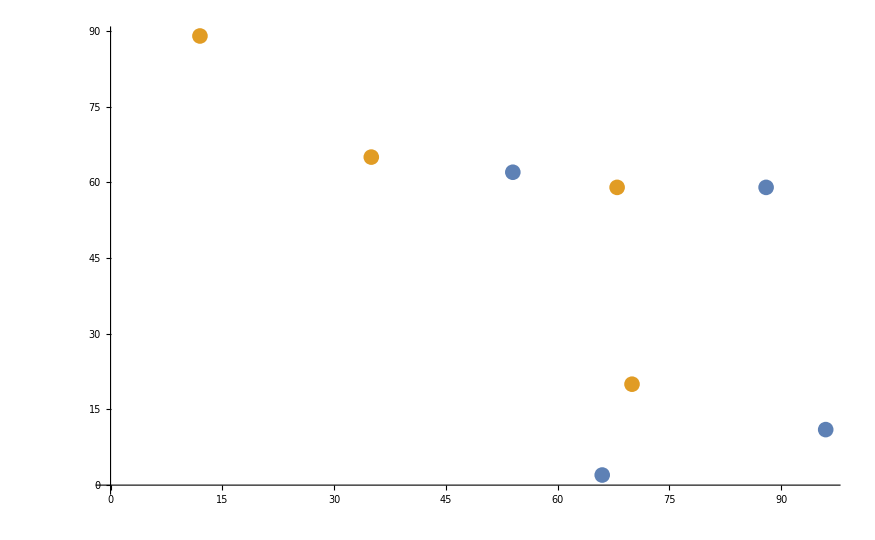

```mathematica
ListPlot[{{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}}]
```

```mathematica
Manipulate[
ListPlot[{{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}}]
,a
```

```mathematica
(1-a)p+a q/.{p->{{88,59},{96,11},{66,2},{54,62}},q->{{70,20},{12,89},{35,65},{68,59}}}
```

{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}}

```mathematica
Manipulate[
ListPlot[{{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}}}]
,{a,0,1}]
```

```mathematica
ListPlot[{}]
```

```mathematica
Manipulate[
ListPlot[{{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}},{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}}}]
,{a,0,1}]
```

```mathematica
TransformationFunction[({{-0.5323652878700678, -0.665026075014054, 60.019615254728286}, {-0.6528933099841486, -0.6498928265701706, 65.0385461008507}, {-0.009729804920875816, -0.010574362547648968, 1.}})][{{88,59},{96,11},{66,2},{54,62}}]
```

{{54.2898,64.0681},{-31.7047,95.0398},{69.9571,61.3269},{55.0201,58.0657}}

```mathematica
Manipulate[
ListPlot[{
{{88,59},{96,11},{66,2},{54,62}},
{{70,20},{12,89},{35,65},{68,59}},
TransformationFunction[({{-0.5323652878700678, -0.665026075014054, 60.019615254728286}, {-0.6528933099841486, -0.6498928265701706, 65.0385461008507}, {-0.009729804920875816, -0.010574362547648968, 1.}})][
{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}}
],
{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}}
}],{a,0,1}]
```

```mathematica
p^(1-a) q^a/.{p->{{88,59},{96,11},{66,2},{54,62}},q->{{70,20},{12,89},{35,65},{68,59}}}
```

{{2^(3-2 a) 11^(1-a) 35^a,20^a 59^(1-a)},{3 2^(5-3 a),11^(1-a) 89^a},{35^a 66^(1-a),2^(1-a) 65^a},{2^(1+a) 17^a 27^(1-a),59^a 62^(1-a)}}

```mathematica
Manipulate[
ListPlot[{
{{88,59},{96,11},{66,2},{54,62}},
{{70,20},{12,89},{35,65},{68,59}},
{{88 (1-a)+70 a,59 (1-a)+20 a},{96 (1-a)+12 a,11 (1-a)+89 a},{66 (1-a)+35 a,2 (1-a)+65 a},{54 (1-a)+68 a,62 (1-a)+59 a}},
{{2^(3-2 a) 11^(1-a) 35^a,20^a 59^(1-a)},{3 2^(5-3 a),11^(1-a) 89^a},{35^a 66^(1-a),2^(1-a) 65^a},{2^(1+a) 17^a 27^(1-a),59^a 62^(1-a)}}
}],{a,0,1}]
```

```mathematica
p^(1-a) q^a/.{p->{{88,59},{96,11},{66,2},{54,62}},q->{{70,20},{12,89},{35,65},{68,59}}}
```

{{2^(3-2 a) 11^(1-a) 35^a,20^a 59^(1-a)},{3 2^(5-3 a),11^(1-a) 89^a},{35^a 66^(1-a),2^(1-a) 65^a},{2^(1+a) 17^a 27^(1-a),59^a 62^(1-a)}}

```mathematica
{70,20}-{88,59}
```

{-18,-39}

```mathematica
Normalize@{-18,-39}
```

{-6/(√205),-13/(√205)}

```mathematica
Outer@{{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}}
```

Outer[{{{88,59},{96,11},{66,2},{54,62}},{{70,20},{12,89},{35,65},{68,59}}}]

```mathematica
FullSimplify[{-6/(√205),-13/(√205)}.Normalize[{2^(3-2 a) 11^(1-a) 35^a,20^a 59^(1-a)}],a∈Reals]
```

-(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a))

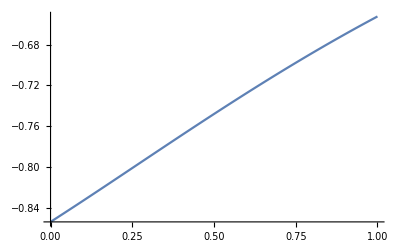

```mathematica
Plot[-(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a)),{a,0,1}]
```

```mathematica
(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a))/.a->1
```

68/(√10865)

```mathematica
(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a))/.a->0
```

259/(√92045)

```mathematica
Integrate[(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a)),{a,0,1}]
```

∫_0^1 (767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a))ⅆa

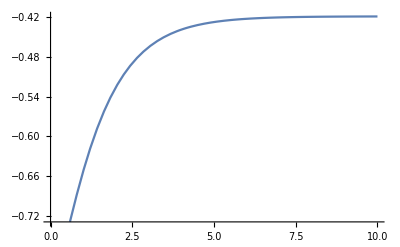

```mathematica
Plot[-(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a)),{a,0,10}]
```

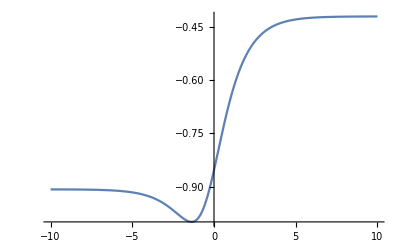

```mathematica
Plot[-(767 176^a+528 413^a)/(√205 √(7744 413^(2 a)+3481 30976^a)),{a,-10,10}]
```

```mathematica
ȳ[x]==y[x]+ϵ η[x]
```

ȳ[x]==y[x]+ϵ η[x]

```mathematica
Dt[ȳ[x]==y[x]+ϵ η[x]]
```

Dt[x] ȳ'[x]==Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x]

```mathematica
Solve[Dt[x] ȳ'[x]==Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x],Dt[x]]
```

{{Dt[x]→-(Dt[ϵ] η[x])/(y'[x]+ϵ η'[x]-ȳ'[x])}}

```mathematica
Solve[Dt[x] ȳ'[x]==Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x],y'[x]]
```

{{y'[x]→(-Dt[ϵ] η[x]-ϵ Dt[x] η'[x]+Dt[x] ȳ'[x])/Dt[x]}}

```mathematica
Solve[Dt[x] ȳ'[x]==Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x],ȳ'[x]]
```

{{ȳ'[x]→(Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x])/Dt[x]}}

```mathematica
TraditionalForm[ȳ'[x]==(Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x])/Dt[x]]
```

ȳ'(x)==(ⅆx y'(x)+ϵ ⅆx η'(x)+η(x) ⅆϵ)/ⅆx

```mathematica
ȳ'[x]==(Dt[ϵ] η[x]+Dt[x] y'[x]+ϵ Dt[x] η'[x])/Dt[x]/.Dt[ϵ]->0
```

ȳ'[x]==(Dt[x] y'[x]+ϵ Dt[x] η'[x])/Dt[x]

```mathematica
ȳ'[x]==Dt[x] y'[x]+ϵ Dt[x] η'[x]
```

ȳ'[x]==Dt[x] y'[x]+ϵ Dt[x] η'[x]

```mathematica
TraditionalForm[ȳ'[x]==Dt[x] y'[x]+ϵ Dt[x] η'[x]]
```

ȳ'(x)==ⅆx y'(x)+ϵ ⅆx η'(x)

```mathematica
(* ȳ'(x)==ⅆx y'(x)+ϵ ⅆx η'(x) *)
```

```mathematica
1
```

1

```mathematica
2
```

2

```mathematica
3
```

3

```mathematica
Dt[f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]]
```

Dt[x] f'[x] f'[f[x]] f'[f[f[x]]] f'[f[f[f[x]]]] f'[f[f[f[f[x]]]]] f'[f[f[f[f[f[x]]]]]] f'[f[f[f[f[f[f[x]]]]]]] f'[f[f[f[f[f[f[f[x]]]]]]]] f'[f[f[f[f[f[f[f[f[x]]]]]]]]] f'[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

```mathematica
Dt[f[f[x]]]
```

Dt[x] f'[x] f'[f[x]]

```mathematica
Dt[x] f'[x] f'[f[x]]==f[x]
```

Dt[x] f'[x] f'[f[x]]==f[x]

```mathematica
Dt[f[x]]==g[f[x]]
```

Dt[x] f'[x]==g[f[x]]

```mathematica
Dt[f[f]]
```

Dt[f] f'[f]

```mathematica
Dt[f]
```

Dt[f]

```mathematica
Dt[Composition[a,b,c][x]]
```

Dt[x] a'[b[c[x]]] b'[c[x]] c'[x]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[x] f'[x]/.x->g[x]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
Dt[x] f'[g[x]] g'[x]/.x->h[x]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
1/(√(x^2-1))
```

1/(√(-1+x^2))

```mathematica
D[1/(√(-1+x^2)), x]
```

-x/((-1+x^2)^(3/2))

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2))
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2))

```mathematica
Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-(x Dt[x])/((-1+x^2)^(3/2))
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]==-(x Dt[x])/((-1+x^2)^(3/2))

```mathematica
f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2))
```

f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2))

```mathematica
DSolve[f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2)),{f[g[h[x]]],g[h[x]],h[x]},{x}]
```

DSolve[f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2)),{f[g[h[x]]],g[h[x]],h[x]},{x}]

```mathematica
f'[g[h[x]]] g'[h[x]] h'[x]==-x/((-1+x^2)^(3/2))
```

```mathematica
f[g[h[x]]]/.{f->Function[x,1/x],g->Function[x, √x]}
```

1/(√h[x])

```mathematica
f[g[h[x]]]/.{f->Function[x,1/x],g->Function[x, √x],h->Function[x, x-1]}
```

1/(√(-1+x))

```mathematica
f[g[hj[[x]]]]/.{f->Function[x,1/x],g->Function[x, √x],h->Function[x, x-1],j->Function[x, x x]}
```

1/(√hj⟦x⟧)

```mathematica
f[g[h[j[x]]]]/.{f->Function[x,1/x],g->Function[x, √x],h->Function[x, x-1],j->Function[x, x x]}
```

1/(√(-1+x^2))

```mathematica
D[{1/x,√x,x-1,x x},x]
```

{-1/x^2,1/(2 √x),1,2 x}

```mathematica
D[1/(√(-1+x^2)), x]
```

-x/((-1+x^2)^(3/2))

```mathematica
Dt[f[g[h[j[x]]]]]
```

Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]

```mathematica
Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]/.{f->Function[x,1/x],g->Function[x, √x],h->Function[x, x-1],j->Function[x, x x]}
```

-(x Dt[x])/((-1+x^2)^(3/2))

```mathematica
Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]/.{j->Function[x, x x]}
```

2 x Dt[x] f'[g[h[x^2]]] g'[h[x^2]] h'[x^2]

```mathematica
Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]/.{j->Function[x, x x],h->Function[x, x-1]}
```

2 x Dt[x] f'[g[-1+x^2]] g'[-1+x^2]

```mathematica
Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]/.{j->Function[x, x x],h->Function[x, x-1],g->Function[x, √x]}
```

(x Dt[x] f'[√(-1+x^2)])/(√(-1+x^2))

```mathematica
{Dt[x], f'[g[h[j[x]]]] ,g'[h[j[x]]], h'[j[x]], j'[x]}/.{f->Function[x,1/x],g->Function[x, √x],h->Function[x, x-1],j->Function[x, x x]}
```

{Dt[x],-1/(-1+x^2),1/(2 √(-1+x^2)),1,2 x}

```mathematica
Product@{Dt[x],-1/(-1+x^2),1/(2 √(-1+x^2)),1,2 x}
```

Product[{Dt[x],-1/(-1+x^2),1/(2 √(-1+x^2)),1,2 x}]

```mathematica
Apply[Product,{Dt[x],-1/(-1+x^2),1/(2 √(-1+x^2)),1,2 x}]
```

∏_(-1/(-1+x^2)) ∏_(1/(2 √(-1+x^2))) ∏_1 ∏_(2 x) Dt[x]

```mathematica
Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2))
```

Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2))

```mathematica
Solve[Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2)),h'[j[x]]]
```

{{h'[j[x]]→-x/((-1+x^2)^(3/2) f'[g[h[j[x]]]] g'[h[j[x]]] j'[x])}}

```mathematica
Solve[Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2)),f'[g[h[j[x]]]]]
```

{{f'[g[h[j[x]]]]→-x/((-1+x^2)^(3/2) g'[h[j[x]]] h'[j[x]] j'[x])}}

```mathematica
Solve[Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2)),x]
```

Solve[Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2)),x]

```mathematica
Solve[Dt[x] f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]] j'[x]==-(x Dt[x])/((-1+x^2)^(3/2)),j'[x]]
```

{{j'[x]→-x/((-1+x^2)^(3/2) f'[g[h[j[x]]]] g'[h[j[x]]] h'[j[x]])}}

```mathematica
2 x==-(x Dt[x])/((-1+x^2)^(3/2))1/(2 √(-1+x^2))-1/(-1+x^2)Dt[x]
```

2 x==-(x Dt[x])/(2 (-1+x^2)^2)-Dt[x]/(-1+x^2)

```mathematica
2 x==-(x Dt[x])/((-1+x^2)^(3/2))1/(2 √(-1+x^2))-1/(-1+x^2)1/Dt[x]
```

2 x==-1/((-1+x^2) Dt[x])-(x Dt[x])/(2 (-1+x^2)^2)